```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames[]
```

{1200.nb,1200_upravene.nb,1400.nb,1500.nb,1600.nb,1800.nb,2000.nb,final-NG-1200-100SK-27BTDC.pdf,NG-1200-100SK-27BTDC.TXT,NG-1400-100SK-27BTDC.TXT,NG-1500-100SK-27BTDC.TXT,NG-1600-100SK-27BTDC.TXT,NG-1800-100SK-27BTDC.TXT,NG-2000-100SK-27BTDC.TXT,piatystlpec-NG-1200-100SK-27BTDC.TXT.txt,piatystlpec-NG-1200-100SK-27BTDC.TXT.xls,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls,tretistlpec-NG-1200-100SK-27BTDC.TXT.txt,tretistlpec-NG-1200-100SK-27BTDC.TXT.xls}

```mathematica
su="NG-1800-100SK-27BTDC.TXT";
```

```mathematica
h=ReadList[su,Table[Number,{5}]];
```

```mathematica
prvystlpec=h[[All,1]];
druhystlpec=h[[All,2]];
tretistlpec=h[[All,3]];
stvrtystlpec=h[[All,4]];
piatystlpec=h[[All,5]];
```

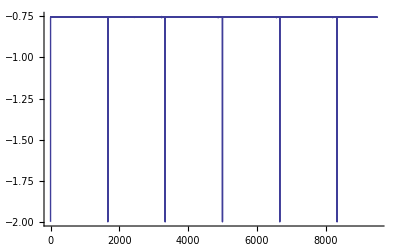

```mathematica
ListLinePlot[druhystlpec[[1;;9500;;1]],PlotRange->All]
```

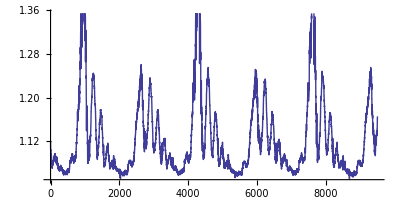

```mathematica
ListLinePlot[tretistlpec[[1;;9500;;1]],AspectRatio->0.5]
```

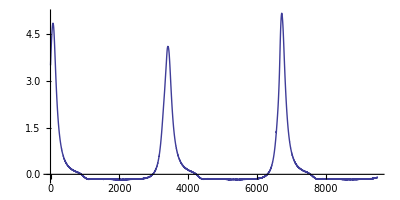

```mathematica
ListLinePlot[stvrtystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

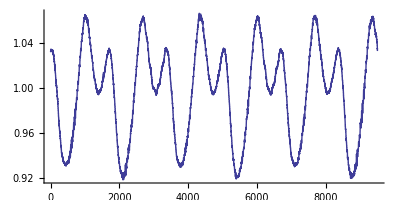

```mathematica
ListLinePlot[piatystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

```mathematica
Length[prvystlpec]
```

1043074

```mathematica
pom3={};
Do[
If[druhystlpec[[i]]<-1.8,AppendTo[pom3, i]],{i,1,Length[druhystlpec]}];
pom4={};
Do[
If[pom3[[i+1]]-pom3[[i]]>10,AppendTo[pom4,pom3[[i]]]],{i,1, Length[pom3]-1}];
pom4
```

{1,1667,3332,4997,6663,8328,9993,11658,13323,14989,16654,18320,19985,21651,23317,24983,26649,28315,29980,31646,33311,34977,36642,38307,39973,41638,43303,44969,46635,48301,49968,51634,53300,54966,56632,58297,59963,61628,63294,64959,66624,68289,69953,71618,73283,74948,76612,78277,79941,81606,83270,84935,86599,88264,89929,91594,93258,94923,96587,98252,99916,101581,103246,104911,106575,108240,109904,111569,113234,114899,116564,118230,119894,121560,123225,124891,126557,128223,129889,131555,133221,134887,136553,138219,139885,141551,143217,144883,146549,148215,149881,151547,153212,154878,156544,158210,159875,161541,163207,164872,166538,168203,169869,171535,173200,174866,176531,178197,179862,181527,183192,184858,186524,188190,189855,191522,193188,194854,196520,198186,199852,201518,203184,204850,206515,208181,209846,211512,213177,214842,216507,218173,219838,221503,223169,224834,226499,228165,229830,231496,233161,234827,236493,238159,239824,241490,243155,244821,246487,248153,249818,251484,253150,254816,256482,258147,259813,261479,263144,264810,266475,268141,269806,271472,273137,274803,276469,278136,279802,281468,283133,284800,286465,288131,289796,291462,293127,294793,296459,298125,299791,301457,303122,304787,306452,308118,309783,311448,313114,314779,316444,318110,319775,321441,323106,324771,326437,328102,329767,331433,333098,334764,336429,338094,339760,341425,343091,344757,346423,348090,349756,351422,353088,354754,356420,358086,359751,361417,363082,364748,366413,368079,369744,371409,373074,374740,376405,378071,379736,381401,383066,384732,386398,388065,389731,391397,393063,394729,396394,398060,399726,401391,403056,404722,406387,408053,409719,411385,413051,414717,416382,418048,419713,421379,423044,424710,426376,428043,429709,431376,433042,434709,436375,438042,439708,441374,443040,444707,446373,448039,449704,451370,453035,454701,456368,458033,459698,461364,463029,464694,466359,468025,469689,471354,473019,474684,476348,478013,479677,481342,483007,484672,486336,488001,489665,491330,492994,494659,496323,497989,499655,501321,502986,504652,506318,507983,509649,511314,512980,514645,516311,517976,519641,521306,522971,524636,526301,527967,529631,531297,532963,534628,536294,537960,539626,541292,542957,544623,546289,547956,549622,551288,552954,554620,556286,557952,559618,561284,562950,564615,566281,567946,569612,571278,572943,574608,576273,577939,579604,581269,582933,584598,586263,587929,589595,591261,592926,594592,596258,597924,599591,601258,602924,604590,606257,607923,609589,611256,612921,614587,616253,617919,619584,621250,622916,624582,626247,627912,629577,631242,632907,634572,636236,637901,639566,641231,642895,644560,646224,647889,649554,651218,652883,654548,656213,657877,659542,661207,662871,664537,666201,667867,669532,671198,672864,674530,676197,677863,679530,681197,682864,684531,686197,687863,689529,691195,692861,694526,696191,697857,699522,701188,702853,704519,706184,707850,709515,711181,712845,714510,716176,717841,719506,721171,722837,724502,726166,727832,729498,731163,732828,734494,736159,737824,739490,741155,742820,744485,746151,747816,749481,751146,752811,754476,756141,757806,759471,761137,762802,764468,766133,767799,769464,771130,772795,774461,776126,777791,779456,781121,782785,784451,786115,787781,789446,791111,792777,794442,796107,797773,799438,801103,802768,804434,806099,807765,809430,811096,812762,814428,816093,817759,819425,821091,822757,824423,826089,827755,829421,831087,832753,834420,836085,837752,839419,841085,842750,844417,846082,847748,849414,851080,852745,854411,856077,857743,859409,861076,862742,864408,866074,867740,869406,871072,872737,874403,876068,877733,879398,881064,882729,884394,886059,887724,889388,891054,892719,894384,896048,897714,899379,901044,902709,904375,906040,907705,909371,911036,912701,914366,916032,917697,919362,921028,922693,924359,926024,927690,929354,931020,932685,934350,936015,937680,939345,941010,942674,944339,946005,947670,949335,951000,952665,954330,955995,957660,959325,960991,962656,964322,965988,967654,969319,970985,972651,974317,975984,977651,979318,980985,982651,984317,985984,987650,989316,990982,992648,994314,995980,997646,999312,1000978,1002643,1004309,1005975,1007641,1009306,1010972,1012638,1014303,1015969,1017635,1019300,1020966,1022632,1024297,1025962,1027628,1029293,1030958,1032624,1034289,1035954,1037619,1039283,1040948}

```mathematica
Length[pom4]
```

626

```mathematica
cyklus={};
Table[AppendTo[cyklus,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus//Length
```

312

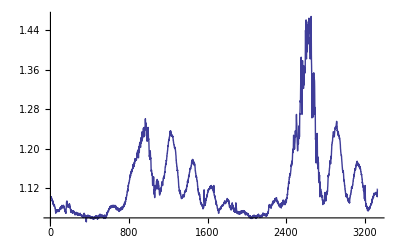
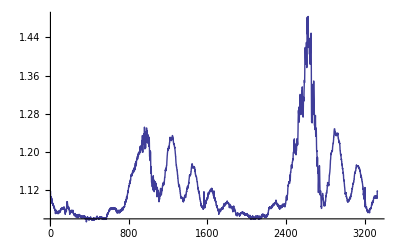
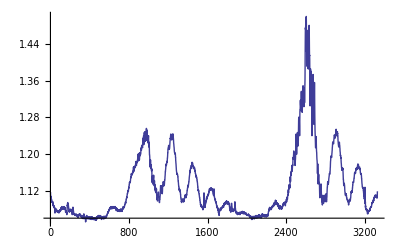
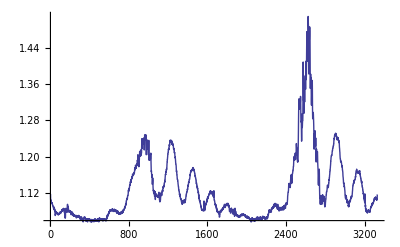
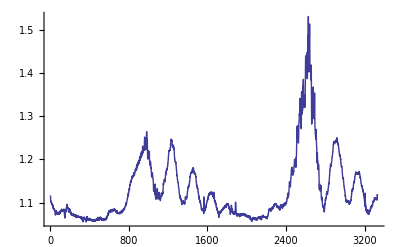
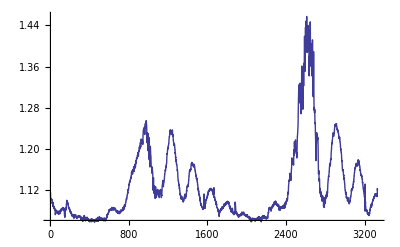
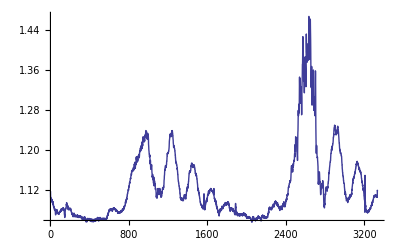
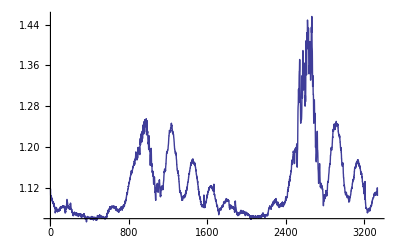

```mathematica
Table[ListLinePlot[cyklus[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]
```

{3331,3332,3331,3332,3332,3332,3333,3333,3332,3332,3331,3332,3332,3333,3334,3333,3332,3332,3332,3331,3330,3331,3330,3330,3330,3330,3331,3330,3330,3330,3331,3330,3330,3331,3332,3331,3332,3333,3333,3333,3333,3333,3333,3333,3333,3332,3333,3332,3332,3332,3333,3332,3332,3331,3332,3333,3333,3333,3333,3333,3333,3332,3332,3331,3332,3331,3332,3332,3332,3332,3333,3332,3332,3333,3332,3333,3332,3333,3332,3332,3332,3332,3334,3333,3333,3332,3332,3332,3333,3333,3331,3332,3331,3332,3332,3332,3331,3332,3332,3332,3331,3332,3333,3334,3333,3333,3333,3332,3332,3332,3331,3332,3332,3331,3332,3334,3333,3333,3332,3332,3332,3332,3333,3333,3332,3332,3332,3334,3334,3334,3334,3333,3334,3333,3332,3332,3333,3332,3331,3332,3330,3331,3330,3330,3331,3330,3330,3330,3331,3333,3332,3332,3332,3332,3332,3331,3331,3332,3331,3332,3333,3333,3332,3334,3333,3333,3333,3333,3332,3332,3333,3331,3332,3331,3330,3332,3333,3332,3333,3335,3333,3334,3334,3332,3333,3332,3333,3331,3331,3331,3330,3331,3330,3330,3330,3331,3330,3331,3331,3331,3332,3333,3334,3335,3335,3333,3333,3332,3332,3332,3332,3332,3332,3330,3332,3331,3332,3331,3332,3332,3331,3332,3331,3332,3331,3331,3331,3332,3332,3332,3332,3332,3331,3331,3331,3331,3331,3332,3332,3331,3332,3332,3332,3333,3332,3333,3333,3333,3333,3334,3333,3334,3333,3332,3333,3332,3333,3334,3333,3333,3333,3332,3331,3332,3331,3331,3331,3331,3331,3331,3332,3331,3332,3331,3332,3332,3332,3332,3331,3331,3331,3331,3330,3332,3331,3331,3331,3332,3332,3333,3332,3333,3335,3335,3333,3334,3333,3333,3333,3333,3332,3333,3332,3332,3333,3332,3332,3332,3331,3332,3331,3330}

```mathematica
pom5=Min[Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]];
pom6=Table[Take[cyklus[[i]],pom5],{i,1,Length[cyklus]}];
```

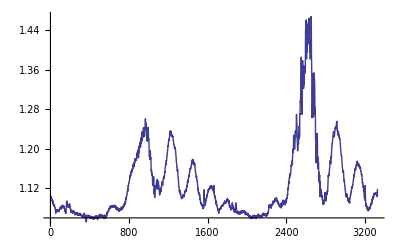
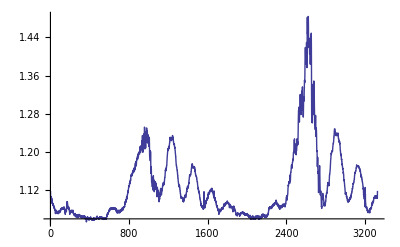
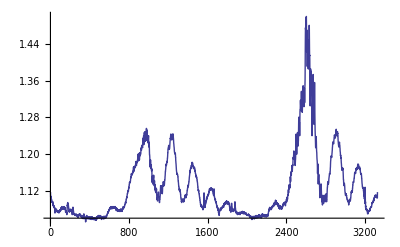
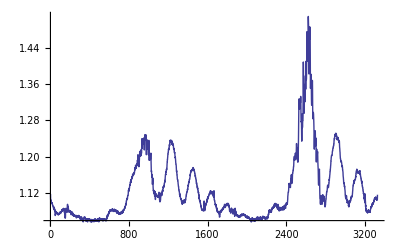
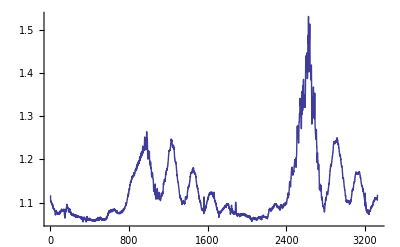
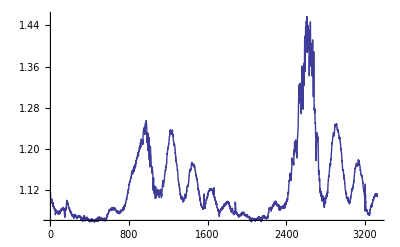
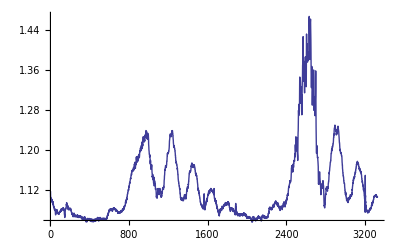
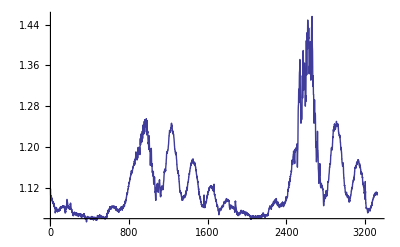

```mathematica
Table[ListLinePlot[pom6[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[pom6]//Dimensions
```

{3330,312}

```mathematica
priemernehodnotydruhystlpec=Table[Mean[pom6[[All,i]]],{i,1,3330}];
```

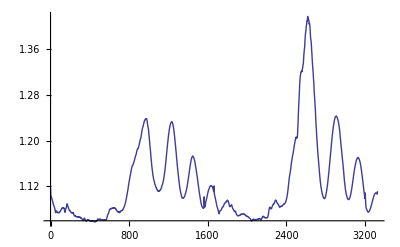

```mathematica
ListLinePlot[priemernehodnotydruhystlpec]
```

```mathematica
cyklus3={};
cyklus4={};
cyklus5={};
Table[AppendTo[cyklus3,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus4,stvrtystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus5,piatystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus3//Length
```

312

```mathematica
Table[ListLinePlot[cyklus3[[i]],PlotRange->All],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

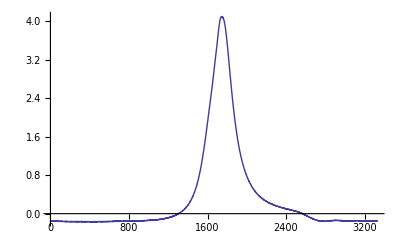
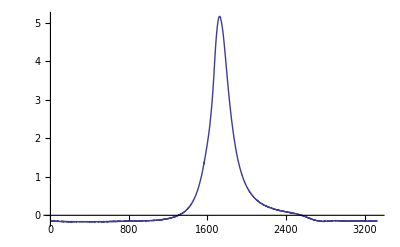
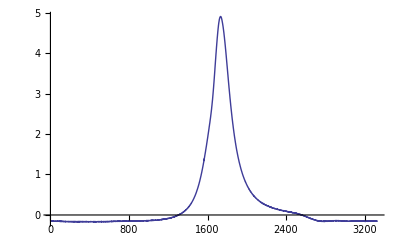
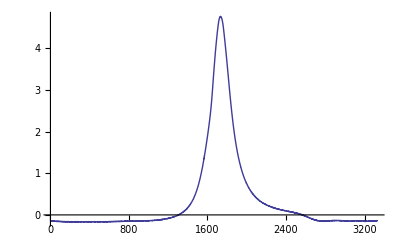
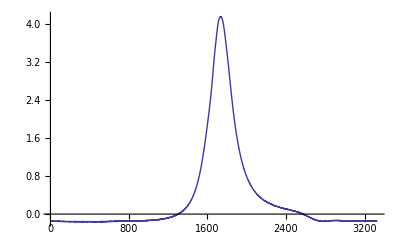
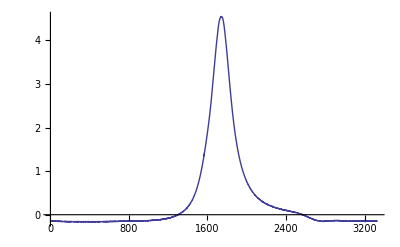
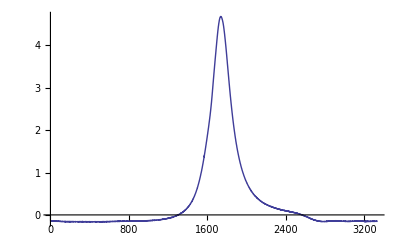
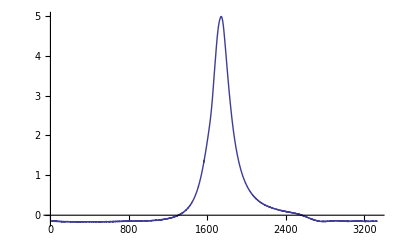

```mathematica
Table[ListLinePlot[cyklus4[[i]],PlotRange->All],{i,1,10}]
```

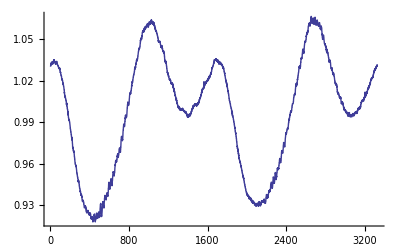
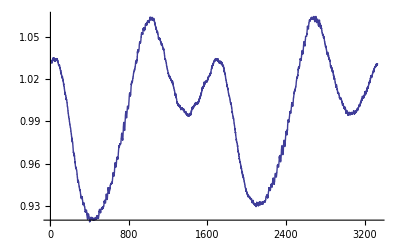
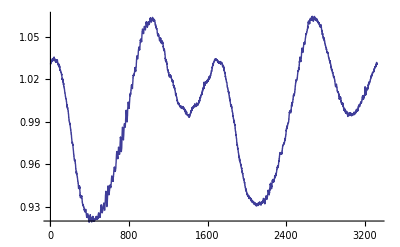
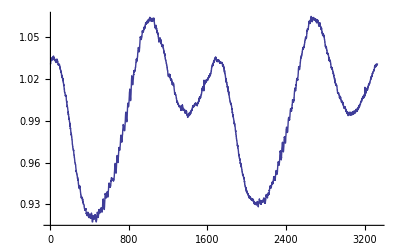
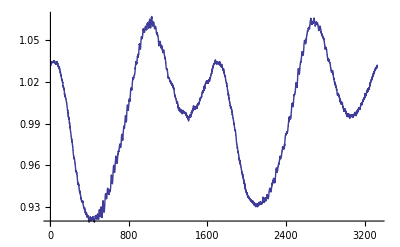
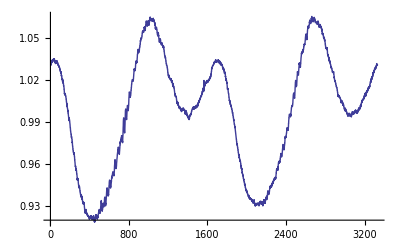
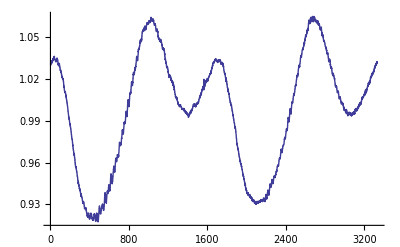
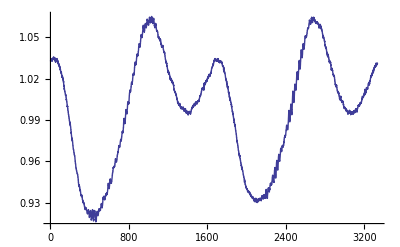

```mathematica
Table[ListLinePlot[cyklus5[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus3[[i]]],{i,1,Length[cyklus]}]
```

{3331,3332,3331,3332,3332,3332,3333,3333,3332,3332,3331,3332,3332,3333,3334,3333,3332,3332,3332,3331,3330,3331,3330,3330,3330,3330,3331,3330,3330,3330,3331,3330,3330,3331,3332,3331,3332,3333,3333,3333,3333,3333,3333,3333,3333,3332,3333,3332,3332,3332,3333,3332,3332,3331,3332,3333,3333,3333,3333,3333,3333,3332,3332,3331,3332,3331,3332,3332,3332,3332,3333,3332,3332,3333,3332,3333,3332,3333,3332,3332,3332,3332,3334,3333,3333,3332,3332,3332,3333,3333,3331,3332,3331,3332,3332,3332,3331,3332,3332,3332,3331,3332,3333,3334,3333,3333,3333,3332,3332,3332,3331,3332,3332,3331,3332,3334,3333,3333,3332,3332,3332,3332,3333,3333,3332,3332,3332,3334,3334,3334,3334,3333,3334,3333,3332,3332,3333,3332,3331,3332,3330,3331,3330,3330,3331,3330,3330,3330,3331,3333,3332,3332,3332,3332,3332,3331,3331,3332,3331,3332,3333,3333,3332,3334,3333,3333,3333,3333,3332,3332,3333,3331,3332,3331,3330,3332,3333,3332,3333,3335,3333,3334,3334,3332,3333,3332,3333,3331,3331,3331,3330,3331,3330,3330,3330,3331,3330,3331,3331,3331,3332,3333,3334,3335,3335,3333,3333,3332,3332,3332,3332,3332,3332,3330,3332,3331,3332,3331,3332,3332,3331,3332,3331,3332,3331,3331,3331,3332,3332,3332,3332,3332,3331,3331,3331,3331,3331,3332,3332,3331,3332,3332,3332,3333,3332,3333,3333,3333,3333,3334,3333,3334,3333,3332,3333,3332,3333,3334,3333,3333,3333,3332,3331,3332,3331,3331,3331,3331,3331,3331,3332,3331,3332,3331,3332,3332,3332,3332,3331,3331,3331,3331,3330,3332,3331,3331,3331,3332,3332,3333,3332,3333,3335,3335,3333,3334,3333,3333,3333,3333,3332,3333,3332,3332,3333,3332,3332,3332,3331,3332,3331,3330}

```mathematica
pom5=Min[Table[Length[cyklus3[[i]]],{i,1,Length[cyklus3]}]];
cyklus3orezany=Table[Take[cyklus3[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus4orezany=Table[Take[cyklus4[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus5orezany=Table[Take[cyklus5[[i]],pom5],{i,1,Length[cyklus3]}];
```

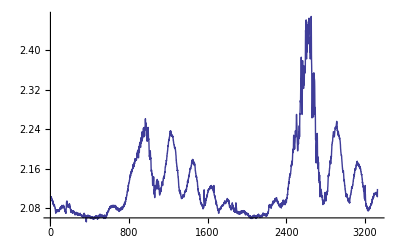
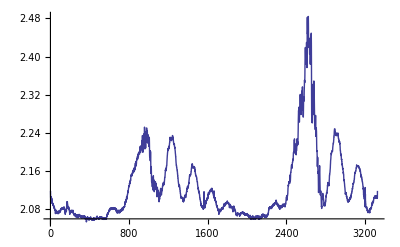
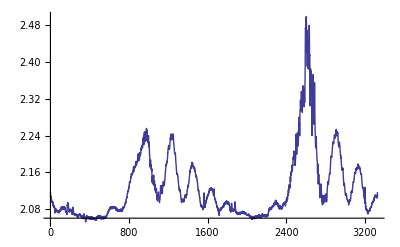
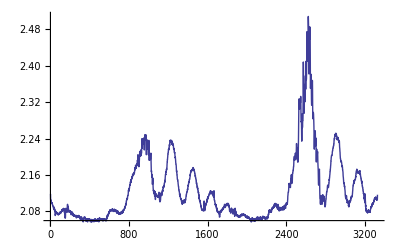
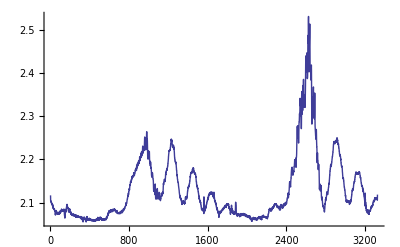
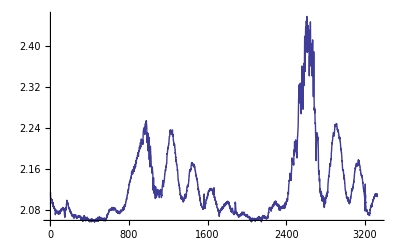
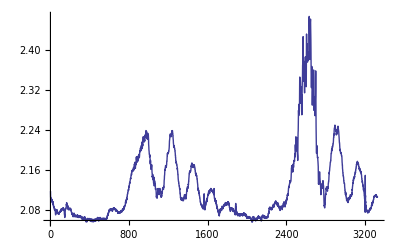
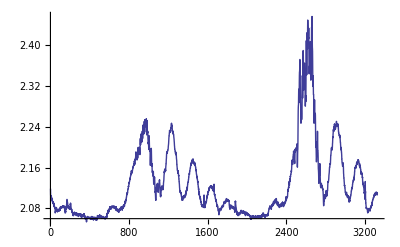

```mathematica
Table[ListLinePlot[cyklus3orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

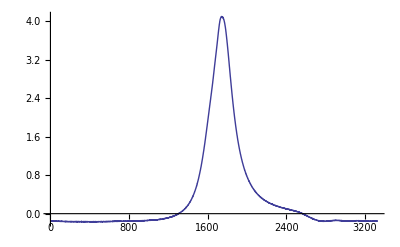
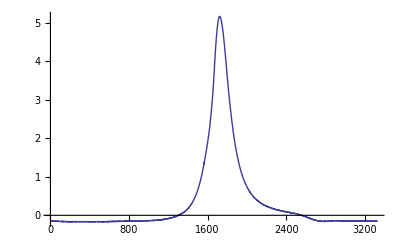
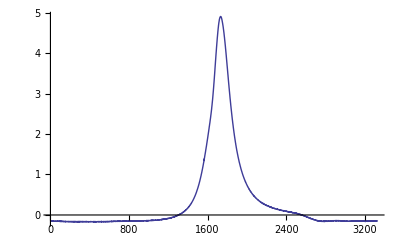
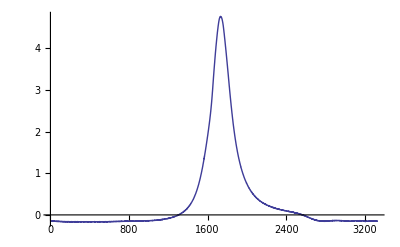
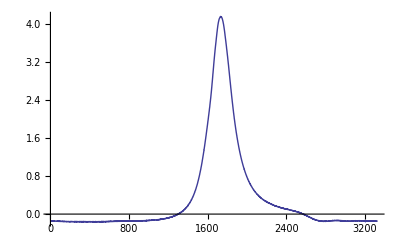
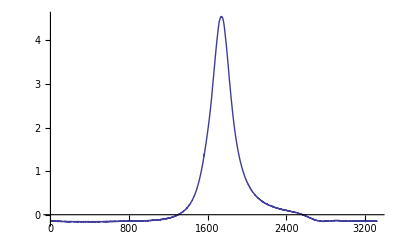
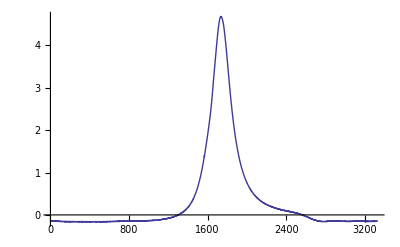
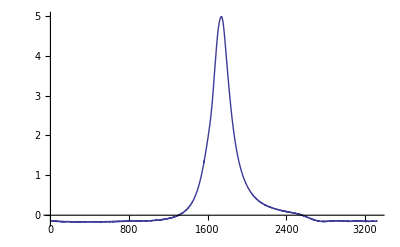

```mathematica
Table[ListLinePlot[cyklus4orezany[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[cyklus3orezany]//Dimensions
```

{3330,312}

```mathematica
priemernehodnoty3stlpec=Table[Mean[cyklus3orezany[[All,i]]],{i,1,3330}];
priemernehodnoty4stlpec=Table[Mean[cyklus4orezany[[All,i]]],{i,1,3330}];
priemernehodnoty5stlpec=Table[Mean[cyklus5orezany[[All,i]]],{i,1,3330}];
```

```mathematica
Length[priemernehodnoty4stlpec]
```

3330

```mathematica
k=0;
x=Table[k=k+720/Length[priemernehodnoty4stlpec]//N,{Length[priemernehodnoty4stlpec]}];
```

```mathematica
obr3=ListLinePlot[priemernehodnoty3stlpec]
```

-Graphics-

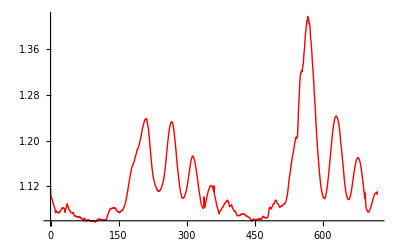

```mathematica
dataobr3=Transpose@{x,priemernehodnoty3stlpec};
obr3a1800=ListLinePlot[dataobr3,PlotStyle->Red]
```

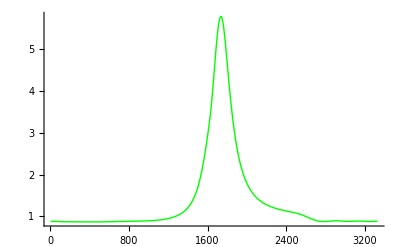

```mathematica
obr4=ListLinePlot[priemernehodnoty4stlpec+1.0335, PlotStyle->Green,PlotRange->All]
```

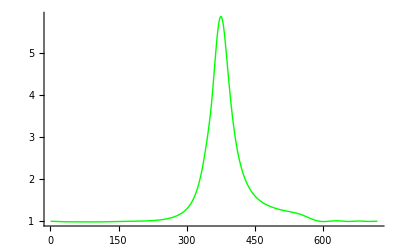

```mathematica
priemernehodnoty4stlpecnove=priemernehodnoty4stlpec+1.1335;
dataobr4=Transpose@{x,priemernehodnoty4stlpecnove};
obr1800va=ListLinePlot[dataobr4,PlotStyle->Green,PlotRange->All]
```

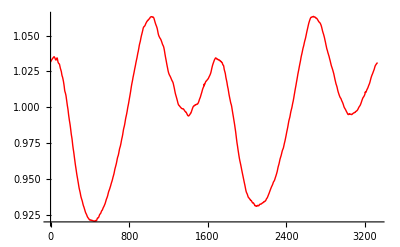

```mathematica
obr5=ListLinePlot[priemernehodnoty5stlpec,PlotStyle->Red]
```

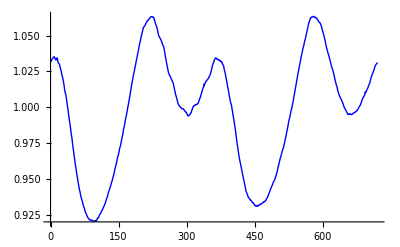

```mathematica
dataobr5=Transpose@{x,priemernehodnoty5stlpec};
obr1800a=ListLinePlot[dataobr5,PlotStyle->Blue]
```

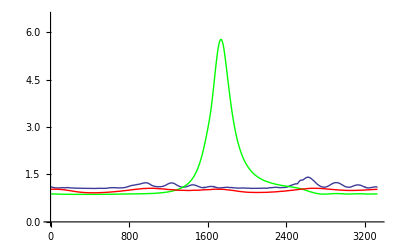

```mathematica
Show[{obr3,obr4,obr5},PlotRange->{{0,3330},{0,6.5}},AxesOrigin->{0,0}]
```

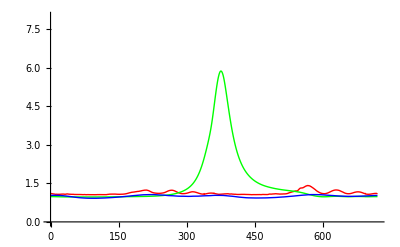

```mathematica
obrfinala=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0,8}},AxesOrigin->{0,0}]
```

```mathematica
brfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},LabelStyle->(FontSize->14),AxesLabel->{"x-axis","y-axis"}]
```

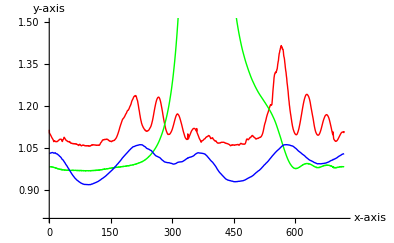

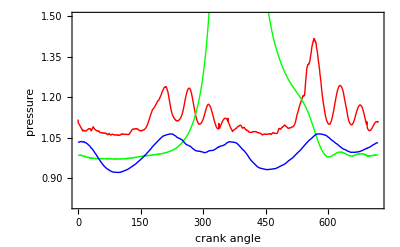

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},PlotRange->{{-3,0},{0,1}},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

-Graphics-